```mathematica
(* parameters *)
qInitial={Pi/8,Pi/3,-3Pi/2}; (* initial disc rotation angles *)
J={1,3,1.6}; (* moments of inertia of the disc *)
r={4,1,2}; (* discs radius *)
centers={{-5,0},{2,3},{2.5,-5}}; (* coordinates of the centers *)
K={2,1}; (* spring stiffness, 1 - red, 2 - blue *)
mt=2; (* modeling time *)
steps=50000; (* time steps *)
dt=mt/steps;
```

```mathematica
(* nearest distance between discs *)
l12=Norm[centers[[2]]-centers[[1]]]-r[[1]]-r[[2]];
l13=Norm[centers[[3]]-centers[[1]]]-r[[1]]-r[[3]];
```

```mathematica
(* func length of the spring by discs rotation angles *)
p12[q1_,q2_]:=Sqrt[(centers[[1,1]]+r[[1]]*Cos[q1]-centers[[2,1]]-r[[2]]*Cos[q2])^2+(centers[[1,2]]+r[[1]]*Sin[q1]-centers[[2,2]]-r[[2]]*Sin[q2])^2];
p13[q1_,q3_]:=Sqrt[(centers[[1,1]]+r[[1]]*Cos[q1]-centers[[3,1]]-r[[3]]*Cos[q3])^2+(centers[[1,2]]+r[[1]]*Sin[q1]-centers[[3,2]]-r[[3]]*Sin[q3])^2];

(* potential energy *)
U[q1_,q2_,q3_]:=(K[[1]]*(p12[q1,q2]-l12)^2)/2+(K[[2]]*(p13[q1,q3]-l13)^2)/2;
(* derivatives of u *)
dUdq1[q1_,q2_,q3_]:=D[U[q1,q2,q3],q1];
dUdq2[q1_,q2_,q3_]:=D[U[q1,q2,q3],q2];
dUdq3[q1_,q2_,q3_]:=D[U[q1,q2,q3],q3];
dUdq={dUdq1,dUdq2, dUdq3};
```

```mathematica
(* create array, containing disc rotation angles *)
q=Table[Table[0,{itq,3}],{itt,steps+1}];
```

```mathematica
(* q01 *)
q01[]:=
(
Do[
Do[
q[[itt+1,itq]]= qInitial[[itq]]
,{itq,3}];
,{itt,0,1,1}];
)
```

```mathematica
(* qij *)
qij[]:=
(
Do[
If[Divisible[itt,1000],Print["steps = ",itt]];
Do[
q[[itt+1,itq]]=N[(dt^2/J[[itq]])*(dUdq[[itq]][q1,q2,q3]/.{q1->q[[itt,1]],q2->q[[itt,2]],q3->q[[itt,3]]})+2q[[itt,itq]]-q[[itt-1,itq]]]
,{itq,3}];
,{itt,2,steps}];
)
```

```mathematica
(* fill the array *)
q01[];
qij[];
```

steps = 1000

steps = 2000

steps = 3000

steps = 4000

steps = 5000

steps = 6000

steps = 7000

steps = 8000

steps = 9000

steps = 10000

steps = 11000

steps = 12000

steps = 13000

steps = 14000

steps = 15000

steps = 16000

steps = 17000

steps = 18000

steps = 19000

steps = 20000

steps = 21000

steps = 22000

steps = 23000

steps = 24000

steps = 25000

steps = 26000

steps = 27000

steps = 28000

steps = 29000

steps = 30000

steps = 31000

steps = 32000

steps = 33000

steps = 34000

steps = 35000

steps = 36000

steps = 37000

steps = 38000

steps = 39000

steps = 40000

steps = 41000

steps = 42000

steps = 43000

steps = 44000

steps = 45000

steps = 46000

steps = 47000

steps = 48000

steps = 49000

steps = 50000

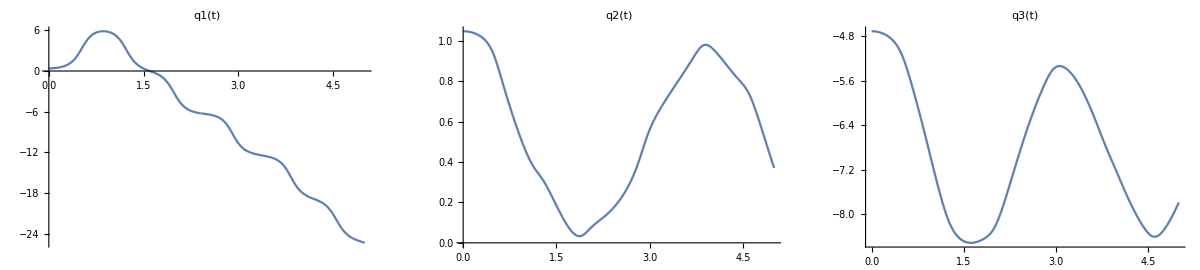

```mathematica
(* plot q1(t),q2(t),q3(t) *)
GraphicsRow[{ListLinePlot[Table[{itt*dt,q[[itt,1]]},{itt,1,steps,1}],DataRange->{0,mt},PlotLabel->"q1(t)"],
ListLinePlot[Table[{itt*dt,q[[itt,2]]},{itt,1,steps,1}],DataRange->{0,mt},PlotLabel->"q2(t)"],
ListLinePlot[Table[{itt*dt,q[[itt,3]]},{itt,1,steps,1}],DataRange->{0,mt},PlotLabel->"q3(t)"]},ImageSize->Full]
```

```mathematica
(* visualization *)

(*  findPlotRange[offset_]:={Min[centers[[All,1]]]-Max[r[[All]]]-offset,Max[centers[[All,1]]]+Max[r[[All]]]+offset};
line1[i_,x_]:=Tan[q[[i,1]]](x-centers[[1,1]])+centers[[1,2]];
line2[i_,x_]:=Tan[q[[i,2]]](x-centers[[2,1]])+centers[[2,2]];
line3[i_,x_]:=Tan[q[[i,3]]](x-centers[[3,1]])+centers[[3,2]];
Manipulate[Plot[{Sqrt[r[[1]]^2-(x-centers[[1,1]])^2]+centers[[1,2]],-Sqrt[r[[1]]^2-(x-centers[[1,1]])^2]+centers[[1,2]],Sqrt[r[[2]]^2-(x-centers[[2,1]])^2]+centers[[2,2]],-Sqrt[r[[2]]^2-(x-centers[[2,1]])^2]+centers[[2,2]],
Sqrt[r[[3]]^2-(x-centers[[3,1]])^2]+centers[[3,2]],-Sqrt[r[[3]]^2-(x-centers[[3,1]])^2]+centers[[3,2]],line1[itt,x],line2[itt,x],line3[itt,x]},{x,findPlotRange[0.2][[1]],findPlotRange[0.2][[2]]},PlotRange->findPlotRange[0.2],AspectRatio->Automatic,PlotStyle->{Black,Black,Black,Black,Black,Black,Blue,Blue,Blue}],{itt,1,steps+1,1}];  *)

Manipulate[Graphics[{Black,Circle[centers[[1,All]],r[[1]]],Black,Circle[centers[[2,All]],r[[2]]],Black,Circle[centers[[3,All]],r[[3]]],Blue,Line[{{-r[[1]]*Cos[q[[itt,1]]]+centers[[1,1]],-r[[1]]*Sin[q[[itt,1]]]+centers[[1,2]]},{-r[[3]]*Cos[q[[itt,3]]]+centers[[3,1]],-r[[3]]*Sin[q[[itt,3]]]+centers[[3,2]]}}],
Red,Line[{{-r[[1]]*Cos[q[[itt,1]]]+centers[[1,1]],-r[[1]]*Sin[q[[itt,1]]]+centers[[1,2]]},{-r[[2]]*Cos[q[[itt,2]]]+centers[[2,1]],-r[[2]]*Sin[q[[itt,2]]]+centers[[2,2]]}}]}],{itt,1,steps+1,1}]
```